```mathematica
Import["Test_Profile_Data.csv",csv]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
SetDirectory["~/Documents/CU/PHYS_4430"]
```

/home/bjorn/Documents/CU/PHYS_4430

```mathematica
data = Import["Test_Profile_Data.csv"]
```

{{Position (m),Photodetector voltage (V)},{-0.00177,0.05},{-0.00167,0.05},{-0.00157,0.05},{-0.00147,0.05},{-0.00137,0.05},{-0.00127,0.05},{-0.00117,0.05},{-0.00107,0.05},{-0.00097,0.05},{-0.00087,0.05},{-0.00077,0.05},{-0.00067,0.05},{-0.00057,0.05},{-0.00047,0.05},{-0.00037,0.05},{-0.00027,0.05},{-0.00017,0.05},{-0.00007,0.05},{0.00003,0.0500002},{0.00013,0.0500018},{0.00023,0.0500155},{0.00033,0.0501095},{0.00043,0.0506425},{0.00053,0.0531332},{0.00063,0.0627308},{0.00073,0.0932276},{0.00083,0.17314},{0.00093,0.345833},{0.00103,0.653619},{0.00113,1.10606},{0.00123,1.6546},{0.00133,2.20314},{0.00143,2.65558},{0.00153,2.96337},{0.00163,3.13606},{0.00173,3.21597},{0.00183,3.24647},{0.00193,3.25607},{0.00203,3.25856},{0.00213,3.25909},{0.00223,3.25918},{0.00233,3.2592},{0.00243,3.2592},{0.00253,3.2592},{0.00263,3.2592},{0.00273,3.2592},{0.00283,3.2592},{0.00293,3.2592},{0.00303,3.2592},{0.00313,3.2592},{0.00323,3.2592},{0.00333,3.2592},{0.00343,3.2592},{0.00353,3.2592},{0.00363,3.2592},{0.00373,3.2592},{0.00383,3.2592},{0.00393,3.2592},{0.00403,3.2592},{0.00413,3.2592},{0.00423,3.2592}}

```mathematica
data[[2;;]]
```

{{-0.00177,0.05},{-0.00167,0.05},{-0.00157,0.05},{-0.00147,0.05},{-0.00137,0.05},{-0.00127,0.05},{-0.00117,0.05},{-0.00107,0.05},{-0.00097,0.05},{-0.00087,0.05},{-0.00077,0.05},{-0.00067,0.05},{-0.00057,0.05},{-0.00047,0.05},{-0.00037,0.05},{-0.00027,0.05},{-0.00017,0.05},{-0.00007,0.05},{0.00003,0.0500002},{0.00013,0.0500018},{0.00023,0.0500155},{0.00033,0.0501095},{0.00043,0.0506425},{0.00053,0.0531332},{0.00063,0.0627308},{0.00073,0.0932276},{0.00083,0.17314},{0.00093,0.345833},{0.00103,0.653619},{0.00113,1.10606},{0.00123,1.6546},{0.00133,2.20314},{0.00143,2.65558},{0.00153,2.96337},{0.00163,3.13606},{0.00173,3.21597},{0.00183,3.24647},{0.00193,3.25607},{0.00203,3.25856},{0.00213,3.25909},{0.00223,3.25918},{0.00233,3.2592},{0.00243,3.2592},{0.00253,3.2592},{0.00263,3.2592},{0.00273,3.2592},{0.00283,3.2592},{0.00293,3.2592},{0.00303,3.2592},{0.00313,3.2592},{0.00323,3.2592},{0.00333,3.2592},{0.00343,3.2592},{0.00353,3.2592},{0.00363,3.2592},{0.00373,3.2592},{0.00383,3.2592},{0.00393,3.2592},{0.00403,3.2592},{0.00413,3.2592},{0.00423,3.2592}}

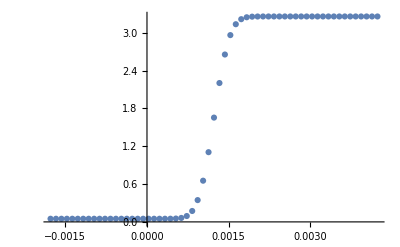

```mathematica
ListPlot[data[[2;;]]]
```

```mathematica
fit =NonlinearModelFit[data[[2;;]],a*Erf[b*(x+c)]+d,{a,b,c,d},x]
```

FittedModel[1.6546+1.6046 Erf[3128.79 (-0.00123+x)]]

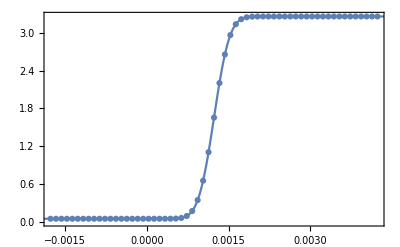

```mathematica
Show[ListPlot[data[[2;;]]],Plot[fit[x],{x,-.002,.005}],Frame->True]
```

```mathematica
fit[parameters]
```

1.6546+1.6046 Erf[3128.79 (-0.00123+parameters)]

```mathematica
Sqrt[2]/3128.79
```

0.000452

```mathematica
fit[[b]]
```

Part::pkspec1: The expression b cannot be used as a part specification.

FittedModel[1.6546+1.6046 Erf[3128.79 (-0.00123+x)]]⟦b⟧

```mathematica
b/.fit
```

ReplaceAll::reps: {FittedModel[1.6546+1.6046 Erf[«2»]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

b/.FittedModel[1.6546+1.6046 Erf[3128.79 (-0.00123+x)]]

```mathematica
fit["BestFitParameters"]
```

{a→1.6046,b→3128.79,c→-0.00123,d→1.6546}

```mathematica
width = Import["gauss_width.csv"]
```

{{Position (m),Power in (W)},{0.006985,0.00569536},{0.0070104,0.00569536},{0.0070358,0.00569536},{0.0070612,0.00566383},{0.0070866,0.00564806},{0.007112,0.00564806},{0.0071374,0.00563229},{0.0071628,0.00561652},{0.0071882,0.00558499},{0.0072136,0.00556922},{0.007239,0.00553769},{0.0072644,0.00550615},{0.0072898,0.00545885},{0.0073152,0.00541154},{0.0073406,0.0053327},{0.007366,0.00526963},{0.0073914,0.00517502},{0.0074168,0.00506465},{0.0074422,0.00492274},{0.0074676,0.00474929},{0.007493,0.00457584},{0.0075184,0.00437086},{0.0075438,0.00410281},{0.0075692,0.00386629},{0.0075946,0.003614},{0.00762,0.00333018},{0.0076454,0.00309366},{0.0076708,0.0027783},{0.0076962,0.00251025},{0.0077216,0.00225796},{0.007747,0.00202144},{0.0077724,0.00178493},{0.0077978,0.00153895},{0.0078232,0.0013245},{0.0078486,0.00111006},{0.007874,0.000946074},{0.0078994,0.000794702},{0.0079248,0.000655945},{0.0079502,0.000529801},{0.0079756,0.000441501},{0.008001,0.000340587},{0.0080264,0.000277515},{0.0080518,0.000227058},{0.0080772,0.0001766},{0.0081026,0.000138758},{0.008128,0.000100915},{0.0081534,0.0000756859},{0.0081788,0.0000504573},{0.0082042,0.0000425733},{0.0082296,0.0000331126},{0.008255,0.000029959},{0.0082804,0.0000204983},{0.0083058,0.0000141911},{0.0083312,0.0000126143},{0.0083566,0.0000110375},{0.008382,9.46074×10^-6},{0.0084074,7.88395×10^-6},{0.0084328,4.73037×10^-6},{0.0084582,3.15358×10^-6},{0.0084836,3.15358×10^-6},{0.008509,1.57679×10^-6},{0.0085344,1.57679×10^-6},{0.0085598,1.57679×10^-6},{0.0085852,1.57679×10^-6}}

```mathematica
width[[2;;]]
```

{{0.006985,0.00569536},{0.0070104,0.00569536},{0.0070358,0.00569536},{0.0070612,0.00566383},{0.0070866,0.00564806},{0.007112,0.00564806},{0.0071374,0.00563229},{0.0071628,0.00561652},{0.0071882,0.00558499},{0.0072136,0.00556922},{0.007239,0.00553769},{0.0072644,0.00550615},{0.0072898,0.00545885},{0.0073152,0.00541154},{0.0073406,0.0053327},{0.007366,0.00526963},{0.0073914,0.00517502},{0.0074168,0.00506465},{0.0074422,0.00492274},{0.0074676,0.00474929},{0.007493,0.00457584},{0.0075184,0.00437086},{0.0075438,0.00410281},{0.0075692,0.00386629},{0.0075946,0.003614},{0.00762,0.00333018},{0.0076454,0.00309366},{0.0076708,0.0027783},{0.0076962,0.00251025},{0.0077216,0.00225796},{0.007747,0.00202144},{0.0077724,0.00178493},{0.0077978,0.00153895},{0.0078232,0.0013245},{0.0078486,0.00111006},{0.007874,0.000946074},{0.0078994,0.000794702},{0.0079248,0.000655945},{0.0079502,0.000529801},{0.0079756,0.000441501},{0.008001,0.000340587},{0.0080264,0.000277515},{0.0080518,0.000227058},{0.0080772,0.0001766},{0.0081026,0.000138758},{0.008128,0.000100915},{0.0081534,0.0000756859},{0.0081788,0.0000504573},{0.0082042,0.0000425733},{0.0082296,0.0000331126},{0.008255,0.000029959},{0.0082804,0.0000204983},{0.0083058,0.0000141911},{0.0083312,0.0000126143},{0.0083566,0.0000110375},{0.008382,9.46074×10^-6},{0.0084074,7.88395×10^-6},{0.0084328,4.73037×10^-6},{0.0084582,3.15358×10^-6},{0.0084836,3.15358×10^-6},{0.008509,1.57679×10^-6},{0.0085344,1.57679×10^-6},{0.0085598,1.57679×10^-6},{0.0085852,1.57679×10^-6}}

```mathematica
data
```

{{Position (m),Photodetector voltage (V)},{-0.00177,0.05},{-0.00167,0.05},{-0.00157,0.05},{-0.00147,0.05},{-0.00137,0.05},{-0.00127,0.05},{-0.00117,0.05},{-0.00107,0.05},{-0.00097,0.05},{-0.00087,0.05},{-0.00077,0.05},{-0.00067,0.05},{-0.00057,0.05},{-0.00047,0.05},{-0.00037,0.05},{-0.00027,0.05},{-0.00017,0.05},{-0.00007,0.05},{0.00003,0.0500002},{0.00013,0.0500018},{0.00023,0.0500155},{0.00033,0.0501095},{0.00043,0.0506425},{0.00053,0.0531332},{0.00063,0.0627308},{0.00073,0.0932276},{0.00083,0.17314},{0.00093,0.345833},{0.00103,0.653619},{0.00113,1.10606},{0.00123,1.6546},{0.00133,2.20314},{0.00143,2.65558},{0.00153,2.96337},{0.00163,3.13606},{0.00173,3.21597},{0.00183,3.24647},{0.00193,3.25607},{0.00203,3.25856},{0.00213,3.25909},{0.00223,3.25918},{0.00233,3.2592},{0.00243,3.2592},{0.00253,3.2592},{0.00263,3.2592},{0.00273,3.2592},{0.00283,3.2592},{0.00293,3.2592},{0.00303,3.2592},{0.00313,3.2592},{0.00323,3.2592},{0.00333,3.2592},{0.00343,3.2592},{0.00353,3.2592},{0.00363,3.2592},{0.00373,3.2592},{0.00383,3.2592},{0.00393,3.2592},{0.00403,3.2592},{0.00413,3.2592},{0.00423,3.2592}}

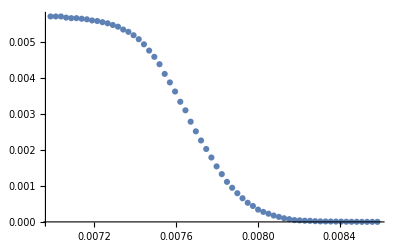

```mathematica
ListPlot[width[[2;;]]]
```

```mathematica
widfit = NonlinearModelFit[width[[2;;]], d-a*Erf[b*(x+c)],{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.919715-1.98188 Erf[1.7319 (0.244132+x)]]

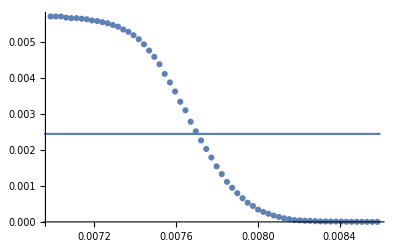

```mathematica
Show[ListPlot[width[[2;;]]],Plot[widfit[x],{x,.0068,.0086},Frame->True]]
```

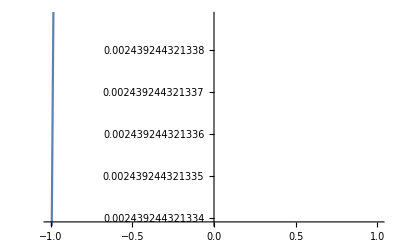

```mathematica
Plot[widfit[x],{x,-1,1}]
```

```mathematica
wid_fit[3]
```

wid_fit[3]